```mathematica
g=1.33/1.586*Sin[h2O];
```

```mathematica
rs=Exp[-2*I*ArcTan[1/(1.586*Cos[g])*Sqrt[1/1.586^2*(Sin[g])^2-1]]]
```

ⅇ^(-2 ⅈ ArcTan[0.630517 Sec[0.838588 Sin[h2O]] √(-1+0.397552 Sin[0.838588 Sin[h2O]]^2)])

```mathematica
rp=-Exp[-2*I*ArcTan[1.586/Cos[g]*Sqrt[1.586^2*(Sin[g])^2-1]]]
```

-ⅇ^(-2 ⅈ ArcTan[1.586 Sec[0.838588 Sin[h2O]] √(-1+2.5154 Sin[0.838588 Sin[h2O]]^2)])

```mathematica
Solve[rs==rp,h2O]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
F=10;
```

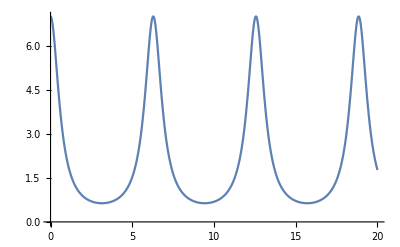

```mathematica
Plot[7/(1+F*(Sin[x/2])^2),{x,0,20}]
```